## Increasing graphs

## Algorithms

```mathematica
horizontalQ[a_Integer, b_Integer, ts_List]:=Block[{result=True},
	Do[
		If[ts[[x]] < ts[[a]] && ts[[x]] < ts[[b]],result=True,result=False;Return[False]],
		{x,a+1,b-1}
	];
	Return[result]
]
```

```mathematica
visibleQ[a_Integer, b_Integer, ts_List]:=Block[{result=True},
	Do[
		If[ts[[x]] >= ts[[a]]+(ts[[b]]−ts[[a]])(x−a)/(b−a),result=False;Return[]],
		{x,a+1,b-1}
	];
	result
]
```

```mathematica
naturalVisibility[series_]:=Block[{visibles},
	visibles={};
	Do[
		Do[
			If[visibleQ[i,j,series],AppendTo[visibles,i->j],Null],
			{j,i+1,Length@series}
		],
		{i,1,Length@series-1}
	];
	Return[visibles]
]
```

```mathematica
horizontalVisibility[series_]:=Block[{visibles},
	visibles={};
	Do[
		Do[
			If[horizontalQ[i,j,series],AppendTo[visibles,i->j],Null],
			{j,i+1,Length@series}
		],
		{i,1,Length@series-1}
	];
	Return[visibles]
]
```

```mathematica
naturalStats[series_]:=Block[{links,degrees,g,nlm},
	links=naturalVisibility[series];
	g=Graph[links[[2;;]]];
	degrees=Counts[VertexDegree[g]]/Length@VertexDegree[g];
	nlm=NonlinearModelFit[Table[{c,Lookup[degrees,c]},{c,Keys[degrees]}],C x^-γ,{γ,C},x];
	nlm["ParameterConfidenceIntervalTable"]
]
```

```mathematica
horizontalStats[series_]:=Block[{links,degrees,g,nlm},
	links=horizontalVisibility[series];
	g=Graph[links[[2;;]]];
	degrees=Counts[VertexDegree[g]]/Length@VertexDegree[g];
	nlm=NonlinearModelFit[Table[{c,Lookup[degrees,c]},{c,Keys[degrees]}],C x^-γ,{γ,C},x];
	nlm["ParameterConfidenceIntervalTable"]
]
```

## Divisors

```mathematica
series=Table[Length@Divisors[x],{x,10000}];
```

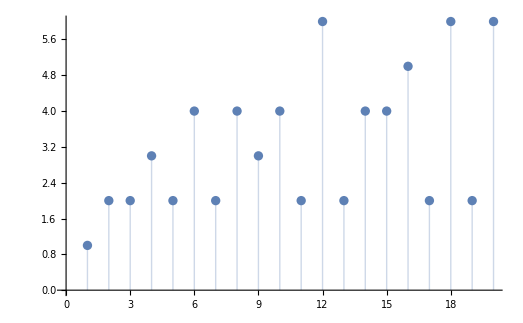

```mathematica
ListPlot[series[[;;20]],Filling->Axis]
```

```mathematica
graphs=Table[Graph[Table[x<->series[[x]],{x,2,l}], VertexLabels->"Name"],{l,2,5000}];
```

```mathematica
Export[NotebookDirectory[]<>"graphs.png",Partition[graphs[[;;10]],3]//TableForm]
```

/Users/blmayer/doctorate/thesis/article-2/graphs.png

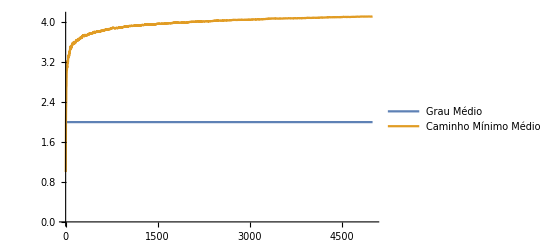

```mathematica
ListLinePlot[{Mean@VertexDegree[#]&/@graphs,MeanGraphDistance/@graphs},PlotLegends->Placed[{"Grau Médio", "Caminho Mínimo Médio"},Below], PlotRange->All]
```

```mathematica
Export["divisors-graphic.pdf",%5]
```

divisors-graphic.pdf

```mathematica
max=Graph[Table[x<->series[[x]],{x,2,Length@series}], VertexLabels->"Name"];
```

```mathematica
{MeanGraphDistance[max],Mean@VertexDegree[max]}//N
```

{4.19149,2.}

```mathematica
MeanGraphDistance[Graph[Table[x<->series[[x]],{x,3,5000}], VertexLabels->"Name"]]//N
```

4.11768

```mathematica
max=Graph[Table[x<->series[[x]],{x,3,Length@series}], VertexLabels->"Name"];
```

```mathematica
{MeanGraphDistance[max],Mean@VertexDegree[max]}//N
```

{4.24815,1.99988}

```mathematica
max=Graph[Table[x<->series[[x]],{x,3,Length@series}], VertexLabels->"Name"];
```

```mathematica
{MeanGraphDistance[max],Mean@VertexDegree[max]}//N
```

{4.25646,1.99989}

```mathematica
distances=Import["/home/blmayer/doctorate/thesis/article-2/distances.csv"]//Flatten;
```

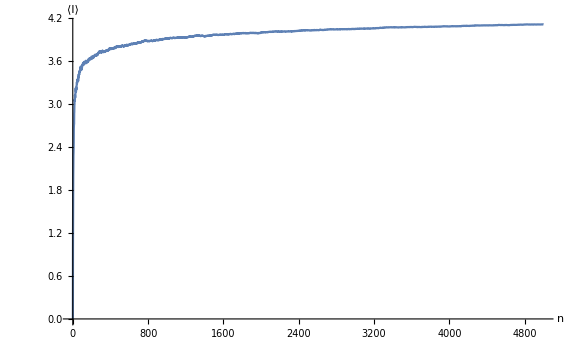

```mathematica
ListLinePlot[distances[[;;5000]], PlotRange->All,LabelStyle->Medium, ImageSize->Large,AxesLabel->{n,⟨l⟩}]
```

```mathematica
Export[NotebookDirectory[]<>"growth-divisors.pdf",%%]
```

/Users/blmayer/doctorate/thesis/article-2/growth-divisors.pdf

```mathematica
distances=MeanGraphDistance/@graphs;
```

```mathematica
distances[[-1]]//N
```

4.19149

```mathematica
distances[[1]]=0;
```

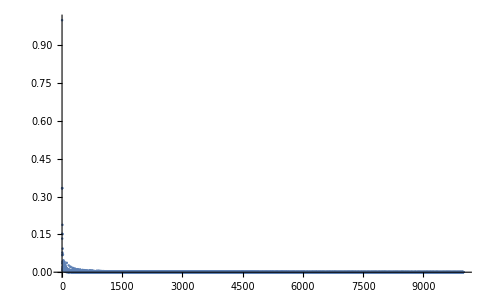

```mathematica
ListPlot[Abs/@Differences@distances,PlotRange->All]
```

```mathematica
nlm=NonlinearModelFit[distances,c+x^d Log[a+b x],{a,b,c,d},x]
```

NonlinearModelFit::nrlnum: The function value {-1372.29+0. ⅈ,-1366.45+0. ⅈ,-1360.14+0. ⅈ,-1353.95+0. ⅈ,-1347.86+0. ⅈ,-1341.65+0. ⅈ,-1335.51+0. ⅈ,-1329.31+0. ⅈ,-1323.19+0. ⅈ,-1317.13+0. ⅈ,-1311.21+0. ⅈ,«30»,-1133.1+0. ⅈ,-1127.58+0. ⅈ,-1122.07+0. ⅈ,-1116.54+0. ⅈ,-1111.05+0. ⅈ,-1105.59+0. ⅈ,-1100.1+0. ⅈ,-1094.64+0. ⅈ,-1089.16+0. ⅈ,«9949»} is not a list of real numbers with dimensions {9999} at {a,b,c,d} = {1643.13,-3.57224,-1379.69,0.944949}.

FittedModel[-1379.69+x^0.944949 Log[1643.13-3.57224 x]]

```mathematica
Plot[nlm[x], {x,1,10000}]
```

-Graphics-

```mathematica
Export["distances.csv",distances//N]
```

distances.csv

## Visibility graphs

```mathematica
links=naturalVisibility[series[[;;100]]];
```

```mathematica
divisorLinks=Table[series[[i[[1]]]]<->series[[i[[2]]]],{i,links}];
```

```mathematica
g=Graph[divisorLinks,DirectedEdges->False,VertexLabels->"Name",GraphLayout->"CircularEmbedding"];
```

```mathematica
hlinks=horizontalVisibility[series[[;;100]]];
```

```mathematica
hdivisorLinks=Table[series[[i[[1]]]]<->series[[i[[2]]]],{i,hlinks}];
```

```mathematica
hg=Graph[hdivisorLinks,DirectedEdges->False,VertexLabels->"Name",GraphLayout->"CircularEmbedding"];
```

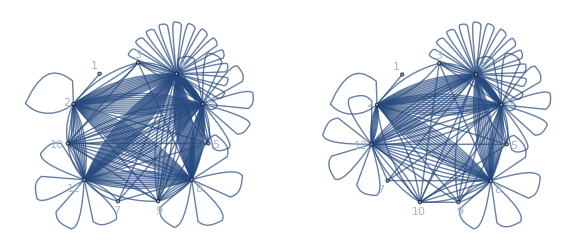

```mathematica
gg=GraphicsGrid[{{g,hg}},ImageSize->Large]
```

```mathematica
Export["divisors-vis-graphs.pdf", %61]
```

divisors-vis-graphs.pdf

```mathematica
degrees=Counts[VertexDegree[g]]/Length@VertexDegree[g]
```

<|2→613/3333,4→56/303,5→1204/9999,10→76/3333,3→655/3333,6→91/1111,13→10/909,7→452/9999,17→47/9999,14→29/3333,24→17/9999,8→371/9999,11→173/9999,12→133/9999,16→20/3333,25→4/3333,9→25/909,15→64/9999,29→7/9999,21→8/3333,18→40/9999,30→2/3333,27→14/9999,42→4/9999,19→1/303,22→2/909,20→38/9999,36→2/3333,26→4/3333,23→7/3333,28→8/9999,34→7/9999,37→1/3333,40→2/9999,46→1/9999,31→7/9999,45→1/9999,54→2/9999,33→4/9999,32→8/9999,43→1/3333,49→1/3333,76→1/9999,39→1/3333,41→1/3333,44→1/9999,38→2/9999,35→4/9999,50→2/9999,61→1/9999,47→1/9999,48→1/9999|>

```mathematica
nlm=NonlinearModelFit[Table[{c,Lookup[degrees,c]},{c,Keys[degrees]}],c x^-γ,{γ,c},x]
```

FittedModel[0.559692/x^1.21489]

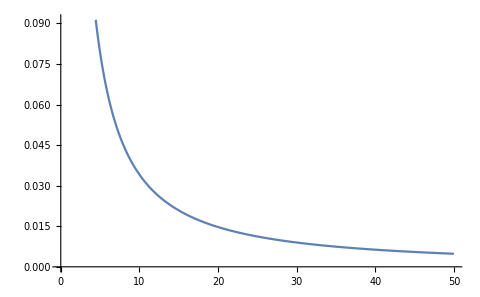

```mathematica
Plot[nlm[x],{x,0,50}]
```

```mathematica
nlm["ParameterConfidenceIntervalTable"]//Normal
```

{{,Estimate,Standard Error,Confidence Interval},{γ,1.21489,0.090935,{1.03224,1.39754}},{c,0.559692,0.0660726,{0.426982,0.692403}}}

```mathematica
VertexDegree[g]//Mean//N
```

5.59656

```mathematica
naturalStats[series[[;;100]]]
```

Join[{{1.21489,0.090935,{1.03224,1.39754}},{0.559692,0.0660726,{0.426982,0.692403}}},4.34343]

## Differences of Divisors

```mathematica
series=Differences@Table[Length@Divisors[x],{x,10001}];
```

```mathematica
links=Table[series[[x]]<->series[[x+1]],{x,Length[series]-1}];
```

```mathematica
g=Graph[links,GraphLayout->"CircularEmbedding"]
```

-Graphics-

## Collatz

```mathematica
collatz[x_]:=If[EvenQ[x],x/2,3x+1]
```

```mathematica
graphs=Table[Graph[Table[x<->collatz[x],{x,l}]],{l,503}];
```

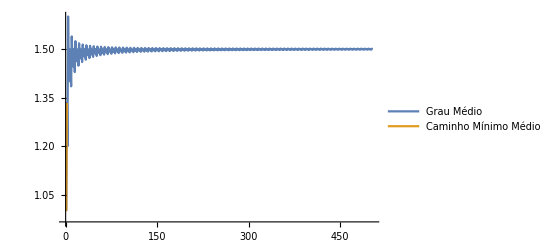

```mathematica
ListLinePlot[{Mean@VertexDegree[#]&/@graphs,MeanGraphDistance/@graphs},PlotLegends->Placed[{"Grau Médio", "Caminho Mínimo Médio"},Below],PlotRange->Full]
```

## Orbit

```mathematica
divGraph=Graph[Table[x<->series[[x]],{x,2,5001}], VertexLabels->"Name"];
```

```mathematica
orbits=Table[GraphDistance[divGraph,2,x], {x,2,5001}];
```

```mathematica
orbits=orbits[[2;;]];
```

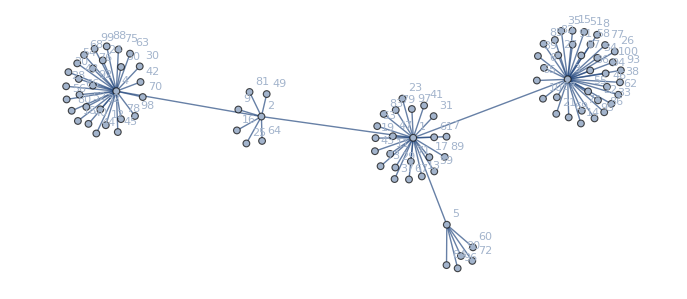

```mathematica
Graph[orbits,VertexLabels->"Name"]
```

```mathematica
links=naturalVisibility[orbits[[2;;]]];
```

```mathematica
divisorLinks=Table[orbits[[i[[1]]]]<->orbits[[i[[2]]]],{i,links}];
```

```mathematica
g=Graph[divisorLinks,DirectedEdges->False,VertexLabels->"Name",GraphLayout->"CircularEmbedding"];
```

```mathematica
hlinks=horizontalVisibility[orbits[[2;;]]];
```

```mathematica
hdivisorLinks=Table[orbits[[i[[1]]]]<->orbits[[i[[2]]]],{i,hlinks}];
```

```mathematica
hg=Graph[hdivisorLinks,DirectedEdges->False,VertexLabels->"Name",GraphLayout->"CircularEmbedding"];
```

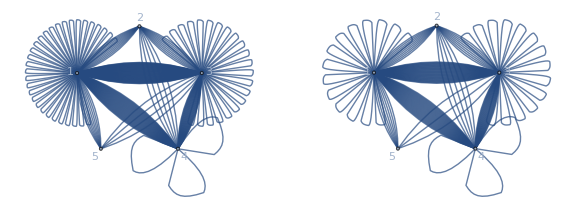

```mathematica
gg=GraphicsGrid[{{g,hg}},ImageSize->Large]
```

```mathematica
Export["orbits-vis-graphs.pdf", %93]
```

orbits-vis-graphs.pdf

```mathematica
ListLinePlot[GraphDistance[graphs[[-1]],2]]
```

```mathematica
naturalStats[GraphDistance[graph,2]]
```

| Estimate | Standard Error | Confidence Interval
γ | 0.556463 | 0.201689 | {0.141886,0.97104}
C | 0.149938 | 0.0485781 | {0.0500838,0.249791}

```mathematica
horizontalStats[GraphDistance[graph,2]]
```

| Estimate | Standard Error | Confidence Interval
γ | 0.353321 | 0.638111 | {-1.20808,1.91472}
C | 0.19898 | 0.154897 | {-0.18004,0.578001}

```mathematica
graphs=Table[Graph[Table[x<->orbits[[x]],{x,l}], VertexLabels->"Name"],{l,5000}];
```

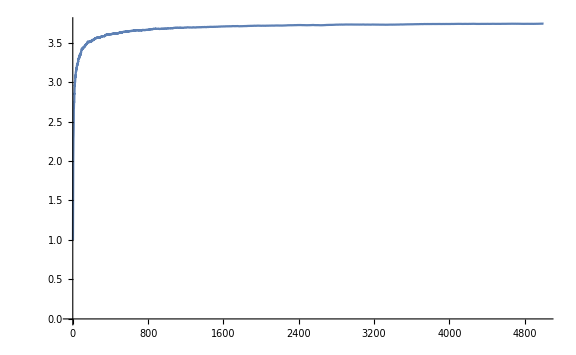

```mathematica
ListLinePlot[{Mean@VertexDegree[#]&/@graphs,MeanGraphDistance/@graphs},PlotLegends->Placed[{"Grau Médio", "Caminho Mínimo Médio"},Bellow], PlotRange->All,LabelStyle->Large, ImageSize->Large]
```

```mathematica
g=-Graphics-;
```

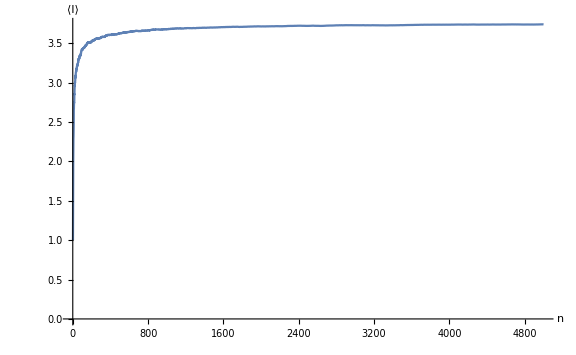

```mathematica
Show[g,LabelStyle->Medium,AxesLabel->{n,⟨l⟩}]
```

```mathematica
orbit=GraphDistance[graphs[[-1]],2];
```

```mathematica
orbit=orbit[[2;;]];
```

```mathematica
orbits=Table[x<->orbit[[x]],{x,Range[Length@orbit]}]
```

{1<->0,2<->2,3<->1,4<->3,5<->1,6<->3,7<->2,8<->3,9<->1,10<->4,11<->1,12<->3,13<->3,14<->2,15<->1,16<->4,17<->1,18<->4,19<->3,20<->3,21<->1,22<->4,23<->2,24<->3,25<->3,26<->4,27<->1,28<->4,29<->1,30<->4,31<->3,32<->3,33<->3,34<->3,35<->1,4928,4964<->4,4965<->1,4966<->5,4967<->1,4968<->3,4969<->3,4970<->5,4971<->1,4972<->4,4973<->4,4974<->4,4975<->5,4976<->4,4977<->3,4978<->5,4979<->3,4980<->4,4981<->4,4982<->3,4983<->3,4984<->5,4985<->1,4986<->5,4987<->3,4988<->4,4989<->4,4990<->5,4991<->1,4992<->4,4993<->3,4994<->4,4995<->3,4996<->5,4997<->1,4998<->5}
 |  |  |  |

```mathematica
orbits[[2]]=2<->1;
```

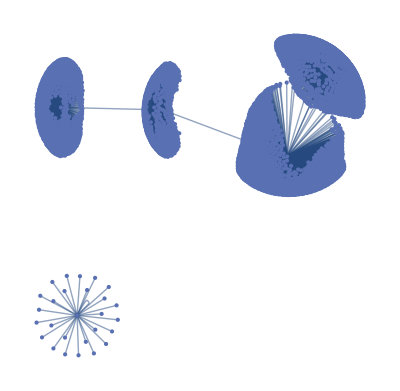

```mathematica
Graph[Table[x<->orbit[[x]],{x,Range[Length@orbit]}]]
```

```mathematica
MeanGraphDistance[Graph[Table[x<->orbit[[x]],{x,Range[3,Length@orbit]}]]]
```

∞

```mathematica
Export[NotebookDirectory[]<>"growth-orbits.pdf",%%]
```

$Aborted

## Mapping

```mathematica
n=10;
```

```mathematica
n=(Length[Divisors[n]])^2+1
```

5

```mathematica
path[x_]:=Block[{k=0,lim=10,n},
n = x;
nodes={};
While[lim>0&&k≠n,
lim--;
k=n;
n= 5Length[Divisors[n]]+1;
AppendTo[nodes,k->n];
];
Return[nodes];
]
```

## Collatz

```mathematica
collatz[x_]:=If[EvenQ[x],x/2,3x+1]
```

```mathematica
collatz[2]
```

1

```mathematica
Table[Length@Divisors[#]&/@NestWhileList[collatz, x, #>1&]//ListLinePlot,{x,100}]
```

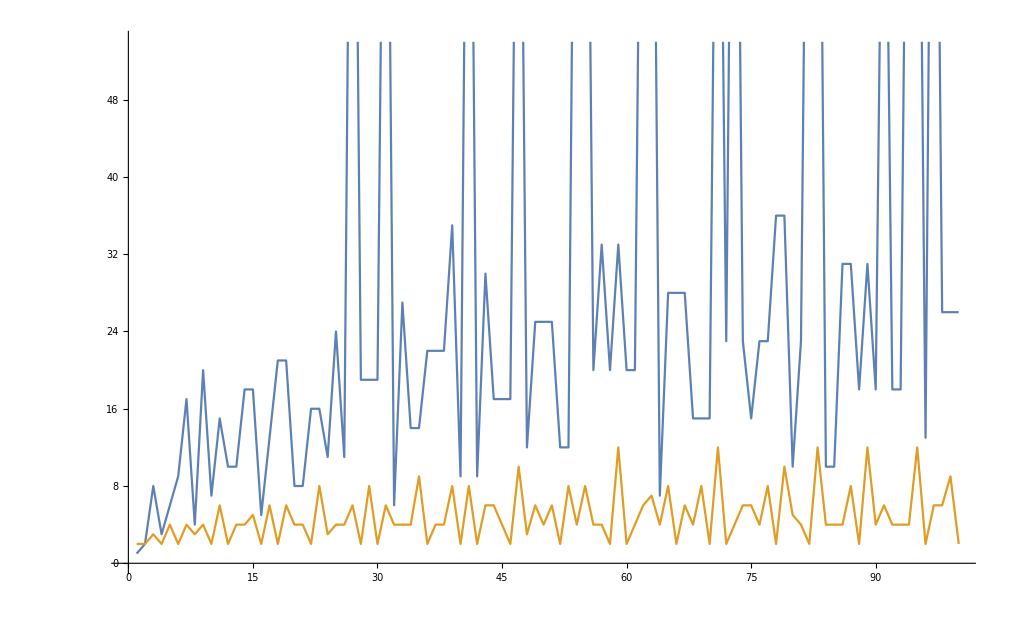

```mathematica
ListLinePlot[{Table[Length@NestWhileList[collatz, x, #>1&],{x,100}],Table[Length@Divisors[x+1],{x,100}]}]
```

```mathematica
Correlation[Table[Length@NestWhileList[collatz, x, #>1&],{x,1000}],Table[Length@Divisors[x+2],{x,1000}]]//N
```

0.0244462

```mathematica
{Mean@VertexDegree[#]&/@graphs,MeanGraphDistance/@graphs}
```

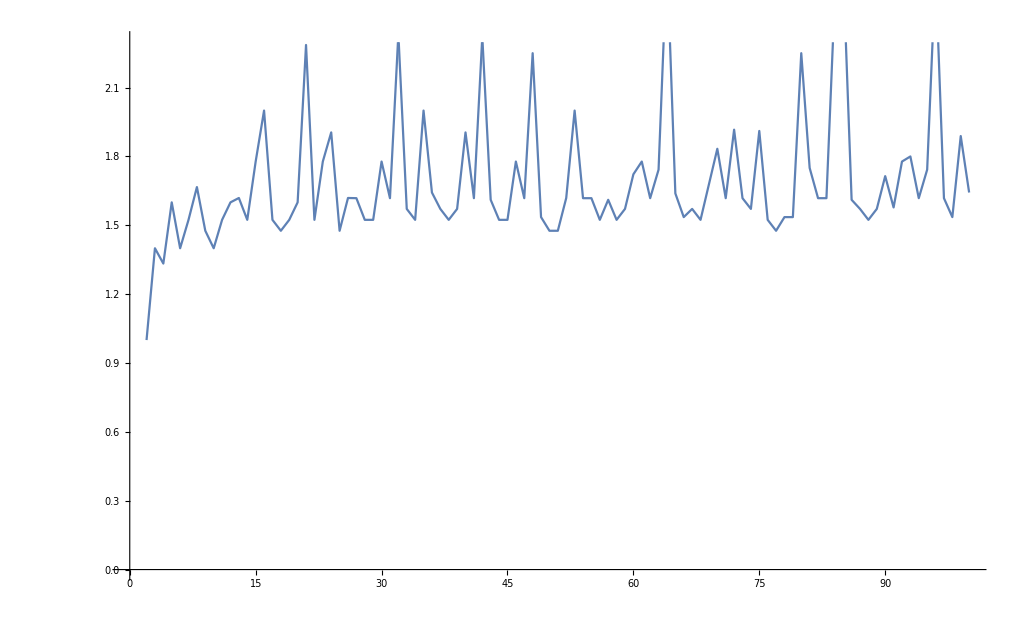

```mathematica
ListLinePlot[MeanGraphDistance/@Table[Length@Divisors@#&/@NestWhileList[collatz,x,#>1&]//listToRule//Graph,{x,100}]]
```

```mathematica
#->#2&@@@Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Table[#[[x]]->#[[x+1]],{x,Length@#-1}]&@Range[10]
```

{1→2,2→3,3→4,4→5,5→6,6→7,7→8,8→9,9→10}

```mathematica
listToRule=Table[#[[x]]<->#[[x+1]],{x,Length@#-1}]&
```

Table[#1⟦x⟧<->#1⟦x+1⟧,{x,Length[#1]-1}]&

```mathematica
listToRule[Range[10]]
```

{1→2,2→3,3→4,4→5,5→6,6→7,7→8,8→9,9→10}